```mathematica
Clear[f,x,y,a,b]
f[x_,y_]:=30x^4y^5
a :={0,1}
b :={-2,2}
Integrate[Integrate[f[x,y],{y,a[[1]],a[[2]]}],{x,b[[1]],b[[2]]}]
```

64

```mathematica
Clear[f,x,y,X,Y]
f[x_,y_]:=E^(x+2y)
Y :={1,Log[3]}
X :={0,Log[2]}
Integrate[Integrate[f[x,y],{y,Y[[1]],Y[[2]]}],{x,X[[1]],X[[2]]}]
```

1/2 (9-ⅇ^2)

```mathematica
Clear[f,x,y,X,Y]
f[x_,y_]:=y x Cos[x]
Y :={-1,1}
X :={0,Pi}
Integrate[Integrate[f[x,y],{y,Y[[1]],Y[[2]]}],{x,X[[1]],X[[2]]}]
```

0

```mathematica
Clear[f,x,y,X,Y]
f[x_,y_]:=7-2x^2-4y^2
Y:={0,1}
X :={0,1}
Integrate[Integrate[f[x,y],{x,X[[1]],X[[2]]}],{y,Y[[1]],Y[[2]]}]
```

5

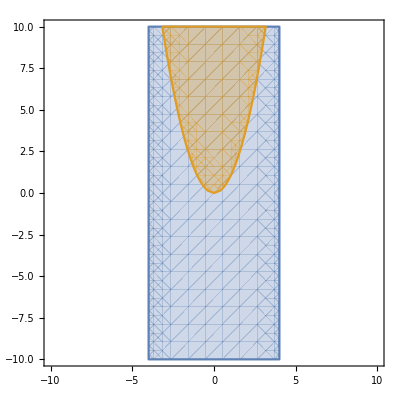

```mathematica
Clear[x,y,size]
size:=10
RegionPlot[{-4 ≤ x≤ 4,x^2≤ y ≤ 16},{x,-size,size},{y,-size,size}]
```

```mathematica
Clear[f,n,x,y,Xsol,X,Y]
" For B the same exponent but 1/n"
equ={x^5,32};
f[x_,y_]:=y== equ[[1]]
Xsol=Solve[f[x,equ[[2]]],x] ;
X={0,x}/.Xsol[[1]];
Y :={equ[[1]],equ[[2]]};
A={{x,X[[1]],X[[2]]},{y,Y[[1]],Y[[2]]}}
```

{{x,0,2},{y,x^5,32}}

```mathematica
Clear[f,x,y,X,Y]
f[x_,y_]:=E^(x+y)
X:={0,Log[y]}
Y :={1,Log[11]}
Integrate[Integrate[f[x,y],{x,X[[1]],X[[2]]}],{y,Y[[1]],Y[[2]]}]
```

ⅇ+11 (-2+Log[11])

```mathematica
Clear[f,x,y,AB,size]
f[x_,y_]:=x^2 E^(x y)
(* Change inner integral to 0,x *)
AB:={0,8,0,x}
(* size:=5
RegionPlot[{AB[[4]] ≤ x≤ AB[[3]],AB[[2]]≤ y ≤ AB[[1]]},{x,-size,size},{y,-size,size}]; *)

Integrate[f[x,y],{x,AB[[1]],AB[[2]]},{y,AB[[3]],AB[[4]]}]
```

1/2 (-65+ⅇ^64)

```mathematica
Clear[z,y,z]
z[x_,y_]:= x^2 + y^2
(* Change outer integral to 0,1/2 of x+y=# *)
AB:={0,3,x,6-x}
Integrate[z[x,y],{x,AB[[1]],AB[[2]]},{y,AB[[3]],AB[[4]]}]
```

108

```mathematica
Clear[f,x,y,X,Y]
f[x_,y_]:=1/(x^3 y)
AB:={∞,6,1,E^-x}
Integrate[f[x,y],{x,AB[[2]],AB[[1]]},{y,AB[[4]],AB[[3]]}]
```

1/6

```mathematica
Clear[f,x,y,X,Y]
f[x_,y_]:=
Y :={-1,1}
X :={0,Pi}
Integrate[Integrate[f[x,y],{y,Y[[1]],Y[[2]]}],{x,X[[1]],X[[2]]}]
Integrate[x+Sqrt[1-x^2],{x,0,1},{y,0,1}]
```

(2+π)/4

```mathematica
Clear[f,x,y,AB]
(* Take the most common factors of number from y ==, find same arrangement, *)
AB:={5,-6,-y^2,y-30}
Integrate[1,{y,AB[[2]],AB[[1]]},{x,AB[[4]],AB[[3]]}]
```

1331/6

{48}

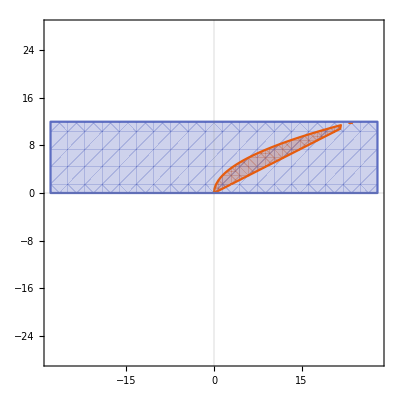

```mathematica
Clear[AB,size]
AB:={12,0,2y,y^2/6}
size:=28
X:={Solve[AB[[1]]==x,y],Solve[AB[[2]]==x,y],Solve[AB[[3]]==x,y],Solve[AB[[4]]==x,y]}
f= y /.X[[4]][[2]];
g= y /.X[[3]];
pX=Solve[f==g,x];
point = g /. pX ;

part =Integrate[1,{y,point[[1]],point[[2]]},{x,AB[[4]],AB[[3]]}]
RegionPlot[{AB[[4]] ≤ x≤ AB[[3]],AB[[2]]≤ y ≤ AB[[1]]},{x,-size,size},{y,-size,size},PlotTheme->"Scientific"]
```

```mathematica
Clear[r,θ,f]
f[r_]:= E^r r
(* Polar is pi/2,0 ln#,0 *)
AB:={Pi/2,0,Log[2],0}
Integrate[f[r],{θ,AB[[1]],AB[[2]]},{r,AB[[3]],AB[[4]]}]
```

1/2 π (-1+Log[4])

```mathematica
Clear[f,x,y,z,AB]
AB:={7,0,7-x,0,7,x+z}
(* CHECK dydzdx with f[x,y,z] *)
Integrate[1,{x,AB[[2]],AB[[1]]},{z,AB[[4]],AB[[3]]},{y,AB[[6]],AB[[5]]}]
```

343/6

```mathematica
Clear[f,x,y,z]
f[y_,z_]:= y Cos[z]
X:={0,3Pi}
Y :={0,Pi}
Z:={0,2}
Integrate[f[y,z],{x,X[[1]],X[[2]]},{y,Y[[1]],Y[[2]]},{z,Z[[1]],Z[[2]]}]
```

3/2 π^3 Sin[2]

```mathematica
Clear[f,x,y,X,Y]
f1[x_,y_]:=0
f2[x_,y_]:= 12 -y     (* f2[x,y] == z *)
g1[x_,y_] :=0
g2[x_,y_]:= 144-y^2 (* g2[x,y] == x *)
(* !! REPLACE ab !! *)
ab:={0,12}  (* number from f1, number from f2 *)
X:={g1[x,y],g2[x,y]}
Y :={ab[[1]],ab[[2]]}
Z:={f1[x,y],f2[x,y]}
Integrate[1,{y,Y[[1]],Y[[2]]},{x,X[[1]],X[[2]]},{z,Z[[1]],Z[[2]]}]
```

8640

```mathematica
Clear[M,My,Mx,AB]
δ:= 2
f[x_]:=2-x^2   
up=x /.Solve[f[x]==x,x];
AB:={up[[2]],0,f[x],x}
M=∫_AB[[2]]^AB[[1]] ∫_AB[[4]]^AB[[3]] δⅆyⅆx         ;
Mx=∫_AB[[2]]^AB[[1]] ∫_AB[[4]]^AB[[3]] y δⅆyⅆx    ;
My=∫_AB[[2]]^AB[[1]] ∫_AB[[4]]^AB[[3]] x δⅆyⅆx    ;

{My/M,Mx/M}
```

{5/14,38/35}

```mathematica
Clear[M,My,Mx,AB]
δ:= 3
f[x_]:=30-x^2   
up=x /.Solve[f[x]==x,x];
AB:={up[[2]],0,f[x],x}
M=∫_AB[[2]]^AB[[1]] ∫_AB[[4]]^AB[[3]] δⅆyⅆx         ;
Mx=∫_AB[[2]]^AB[[1]] ∫_AB[[4]]^AB[[3]] y δⅆyⅆx    ;
My=∫_AB[[2]]^AB[[1]] ∫_AB[[4]]^AB[[3]] x δⅆyⅆx    ;

{My/M,Mx/M}
```

{85/46,310/23}

```mathematica
Clear[M,My,Mx,AB]
δ:= 18x+y+9
f[x_]:=2-x  
up=x /.Solve[f[x]==x,x];
AB:={up,0,f[x],x}
M=∫_AB[[2]]^AB[[1]] ∫_AB[[4]]^AB[[3]] δⅆyⅆx         ;
Mx=∫_AB[[2]]^AB[[1]] ∫_AB[[4]]^AB[[3]] y δⅆyⅆx    ;
My=∫_AB[[2]]^AB[[1]] ∫_AB[[4]]^AB[[3]] x δⅆyⅆx    ;

{My/M,Mx/M}
```

{{19/48},{97/96}}

```mathematica
Clear[a,b,c,δ,Ix,Iy,Iz,fx,fy,fz]
a =2; b=3; c=2; δ=1;
fx [y_,z_]:=(y^2+z^2 )δ    (* dx dy dz *)
fy[x_,z_]:= (x^2 + z^2 )δ   (* dx dy dz *)
fz[x_,y_]:=(x^2+y^2)δ      (* dx dy dz *)
Ix = Integrate[fx[y,z],{z,0,c},{y,0,b},{x,0,a}]
Iy = Integrate[fy[x,z],{z,0,c},{y,0,b},{x,0,a}]
Iz = Integrate[fz[x,y],{z,0,c},{y,0,b},{x,0,a}]
```

52

32

52

```mathematica
Clear[f,r,z,θ,AB]
AB:={Pi,0,1,0,Sqrt[2-r^2],r}
∫_AB[[2]]^AB[[1]] ∫_AB[[4]]^AB[[3]] ∫_AB[[6]]^AB[[5]] r  ⅆzⅆrⅆθ
```

2/3 (-1+√2) π

```mathematica
Clear[plot1,plot2,f,x,y,v,u,y1,y2,y3,y4,X1,Y1,X,Y]
u1:= 2x-y
v1:= 3x+y
p1:={0,0}
p2:={1,2}
p3:={1,-3}
f[x_,y_] := 2x^2+7 x y + 3y^2
(* fix mathematica errors *)
X =0;Y=0;
X1 =x/.Solve[v1==v,x][[1]][[1]];
Y1 = u1 /. x-> X1;
"Y"
Y =y /.Solve[Y1==u,y] [[1]]
"X"
X = X1 /. y -> Y  //Simplify
dXv= D[X,v];
dXu=D[X,u];
dYu= D[Y,u];
dYv = D[Y,v];
"J"
J = dXu dYv - dYu dXv
(* y - y1 == (y2-y1 / x2-x1)*(x-x1)   *)
ab := y-p1[[2]]==((p3[[2]]-p1[[2]])/(p3[[1]]-p1[[1]])) * (x - p1[[1]])
(* division by zero corrected as 0, change if points will not equal 0 *)
bc := y-p2[[2]]==( 0 ) * (x - p2[[1]]) //FullSimplify
sol={ab[[2]],bc[[2]]};
uSol =Solve[Y==X,u];
equ = Y==sol[[1]] /. x-> X     ;
vSol =Solve[equ,v];
xSol =Solve[X==bc[[2]],v] //FullSimplify;
ploT = v /. xSol;
pl1=Graphics[Line[{p1,p2,p3,p1}],Frame->True];
pl2 =ContourPlot[ploT,{u,0,3},{v,0,3},ImageSize->{250},RegionFunction->Function[{u,v},0<u &&0<v]];
Show[pl1,pl2];
(*right facing 30,30,90 triangle *)
```

Y

1/5 (-3 u+2 v)

X

(u+v)/5

J

1/5

```mathematica
Clear[plot1,plot2,f,x,y,v,u,y1,y2,y3,y4,X1,Y1,X,Y]
u1:= 2x+y
v1:= x+3y
y1:= -2x+1
y2:= -2x+2
y3:= -(1/3)x
y4:= -(1/3)x + 3
f[x_,y_] := 2x^2+7 x y + 3y^2
(* fix mathematica errors *)
X =0;Y=0;
(*size := 10
plot1=ContourPlot[{y1,y2,y3,y4},{x,-size,size},{y,-size,size},AspectRatio->Automatic,ImageSize->{250}];
plot2=ContourPlot[1,{x,0,5},{y,0,5},AspectRatio->Automatic,RegionFunction->Function[{x,y},1<x y<2 &&1<x y^2<2],ImageSize->{250},PlotPoints->100];
Show[plot1,plot2];*)

X1 =x/.Solve[v1==v,x][[1]][[1]];
Y1 = u1 /. x-> X1;
Y =y /.Solve[Y1==u,y] [[1]];
X = X1 /. y -> Y  //Simplify;
dXv= D[X,v];
dXu=D[X,u];
dYu= D[Y,u];
dYv = D[Y,v];
J = dXu dYv - dYu dXv;
U1= Y == y1 /. x -> X //Simplify;
U2 = Y == y2 /. x-> X //Simplify;
V1 = Y == y3 /. x-> X //Simplify;
V2 = Y == y4 /. x-> X //Simplify;
fxy = f[X,Y]  //FullSimplify;
Integrate[ fxy*J,{u,U1[[2]],U2[[2]]},{v,V1[[2]],V2[[2]]}]
```

243/20